```mathematica
Animate[Grid[Partition[Table[Style[i,Bold,Larger,If[i>j,Black,If[PrimeQ@i,Blue,Gray]]],{i,100}],10],Spacings->{1,1}],{j,0,100},Paneled->False]
```

```mathematica
Function[p,N[{p Cos[p],p Sin[p]}]][2]
```

{-0.832294,1.81859}

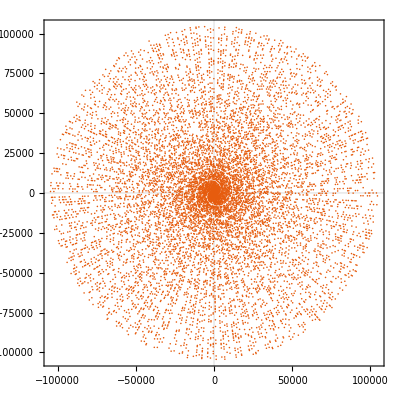

```mathematica
ListPlot[Function[p,N@{p Cos[p],p Sin[p]}]/@Table[Prime[n],{n,10000}],AspectRatio->1,ImageSize->Full,PlotTheme->"Scientific"]
```

```mathematica
s=ListPointPlot3D[Function[p,N@{p Cos[p]/Prime[5000],p Sin[p]/Prime[5000],Log[p]}]/@Table[Prime[n],{n,5000}],AspectRatio->1,PlotTheme->"Business",Boxed->False,Axes->False];
With[{obj=s},Animate[Show[obj,SphericalRegion->True,ViewVector->{Cos[t],Sin[t],12}],{t,0,2Pi}]]
```

```mathematica
co2[k_]:=Sum[1,{n,PrimePi[Power[k,(3)^-1]]},{m,n,PrimePi[k/Prime[n]^2]},{l,m,PrimePi[k/(Prime[n]Prime[m])]}]
AbsoluteTiming[co2[100]]
```

{0.000142758,22}

```mathematica
特殊矩阵
```

```mathematica
data=WolframAlpha["China GDP per capita",{{"History:GDP:WorldDevelopmentData",1},"TimeSeriesData"}][[-6;;-1]]
UnitConvert[Quantity[1,"USDollars"],"ChineseYuan"]
edist=QuantityDistribution[DagumDistribution[5.755534907646728,2.6649335249182378,23588.49207344965],Quantity[, "USDollars"]]
ListPlot[{RandomVariate[edist,100],{{0,Median[edist]},{100,Median[edist]}}},Filling->{1->Axis},Joined->{False,True},AxesOrigin->{0,20000},AxesLabel->Automatic]
```

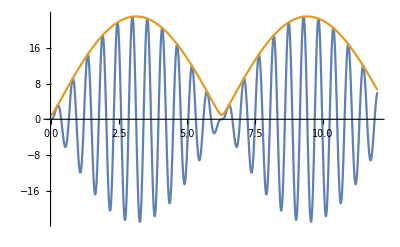

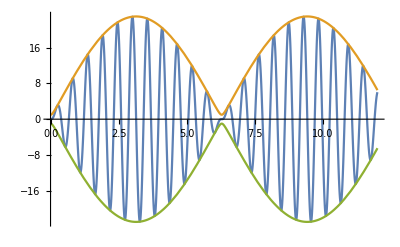

```mathematica
HilbertTransform[f_,u_,t_]:=1/Pi FullSimplify[Convolve[f,1/u,u,t,PrincipalValue->True]];
f[t_]:=12 Sin[11 t]-11 Sin[12 t];
h=HilbertTransform[f[t],t,u];
Plot[{f[t],Abs[f[t]+I (h/.u->t)]},{t,0,12}]
z=Abs[f[t]+I (h/.u->t)];
Plot[{f[t],z,-z},{t,0,12}]
```

SetDelayed::write: (-12 Cos[11 u]+11 Cos[12 u])[t_] 中的标签 Plus 被保护.

$Failed

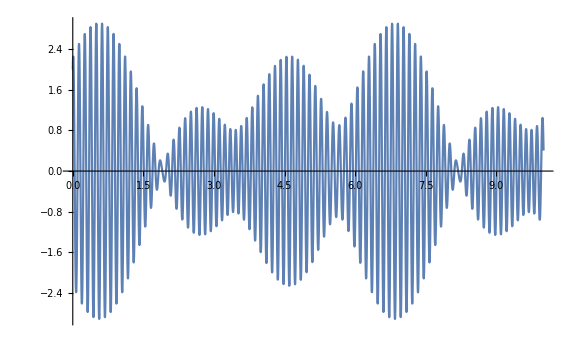

(-12 Cos[11 u]+11 Cos[12 u])[t]

```mathematica
Manipulate[Plot[{Cos[a*t]+Cos[b*t],2*Cos[(b-a) t/2],-2*Cos[(b-a) t/2]},{t,0,10},PlotStyle->{Directive[Opacity[0.7]],Directive[Black,Thick],Directive[Black,Thick]}],{{a,20},1,50},{{b,21},1,50}]
f[t_]:=Cos[50 t]+Cos[51 t]+Sin[53 t] (*more sinusoids=more fun*)
g[t_]:=Evaluate@HilbertTransform[f[τ],τ,t]
h[t_]:=Abs[f[t]+I g[t]]
Plot[{f[t],h[t],-h[t]},{t,0,10},ImageSize->Large,PlotPoints->100,PlotStyle->{Automatic,Black,Black}]
ComplexExpand[h[t]]//FullSimplify
```